```mathematica
SetDirectory[NotebookDirectory[]];
t1 = Import["oned.h5", {"Datasets", "/1/t"}];
meanchange1 = Import["oned.h5", {"Datasets", "/1/mean_change"}];
stderrchange1 = Import["oned.h5", {"Datasets", "/1/stderr_change"}];
ResetDirectory[];
SetDirectory[NotebookDirectory[]];
t2 = Import["oned.h5", {"Datasets", "/2/t"}];
meanNtot2 = Import["oned.h5", {"Datasets", "/2/mean_Ntot"}];
meanNNtot2 = Import["oned.h5", {"Datasets", "/2/mean_NNtot"}];
stderrNtot2 = Import["oned.h5", {"Datasets", "/2/stderr_Ntot"}];
stderrNNtot2 = Import["oned.h5", {"Datasets", "/2/stderr_NNtot"}];
ResetDirectory[];
SetDirectory[NotebookDirectory[]];
t3 = Import["oned.h5", {"Datasets", "/3/t"}];
meanXinitabs3 = Import["oned.h5", {"Datasets", "/3/mean_Xinitabs"}];
meanXinitarg3 = Import["oned.h5", {"Datasets", "/3/mean_Xinitarg"}];
meanXtabs3 = Import["oned.h5", {"Datasets", "/3/mean_Xtabs"}];
meanXtarg3 = Import["oned.h5", {"Datasets", "/3/mean_Xtarg"}];
meanXabs3 = Import["oned.h5", {"Datasets", "/3/mean_Xabs"}];
meanXarg3 = Import["oned.h5", {"Datasets", "/3/mean_Xarg"}];
stderrXinitabs3 = Import["oned.h5", {"Datasets", "/3/stderr_Xinitabs"}];
stderrXinitarg3 = Import["oned.h5", {"Datasets", "/3/stderr_Xinitarg"}];
stderrXtabs3 = Import["oned.h5", {"Datasets", "/3/stderr_Xtabs"}];
stderrXtarg3 = Import["oned.h5", {"Datasets", "/3/stderr_Xtarg"}];
stderrXabs3 = Import["oned.h5", {"Datasets", "/3/stderr_Xabs"}];
stderrXarg3 = Import["oned.h5", {"Datasets", "/3/stderr_Xarg"}];
ResetDirectory[];

declaredVariables={"t1", "meanchange1", "stderrchange1", "t2", "meanNtot2", "meanNNtot2", "stderrNtot2", "stderrNNtot2", "t3", "meanXinitabs3", "meanXinitarg3", "meanXtabs3", "meanXtarg3", "meanXabs3", "meanXarg3", "stderrXinitabs3", "stderrXinitarg3", "stderrXtabs3", "stderrXtarg3", "stderrXabs3", "stderrXarg3"}
```

{t1,meanchange1,stderrchange1,t2,meanNtot2,meanNNtot2,stderrNtot2,stderrNNtot2,t3,meanXinitabs3,meanXinitarg3,meanXtabs3,meanXtarg3,meanXabs3,meanXarg3,stderrXinitabs3,stderrXinitarg3,stderrXtabs3,stderrXtarg3,stderrXabs3,stderrXarg3}

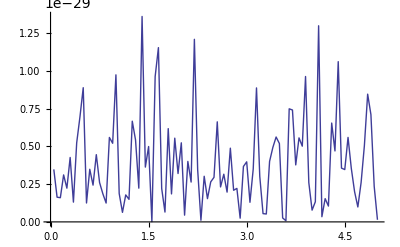

```mathematica
ListLinePlot[Transpose[{t1,meanchange1}]]
```

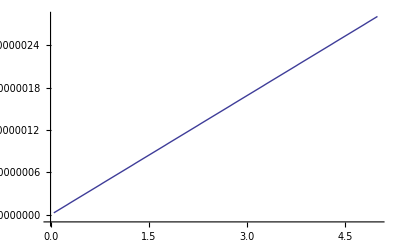

```mathematica
ListLinePlot[Transpose[{t2,meanNtot2}]]
```

```mathematica
ListLinePlot[Transpose[{t2,meanNNtot2}]]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{t3,meanXtabs3}]]
```

-Graphics-

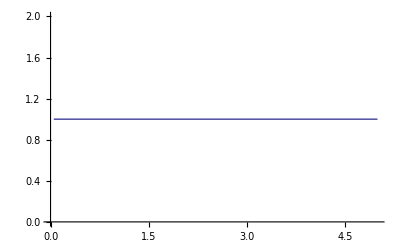

```mathematica
ListLinePlot[Transpose[{t3,meanXinitabs3}]]
```

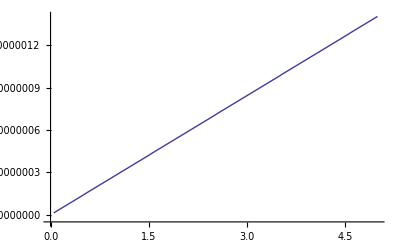

```mathematica
ListLinePlot[Transpose[{t3,meanXabs3}]]
```

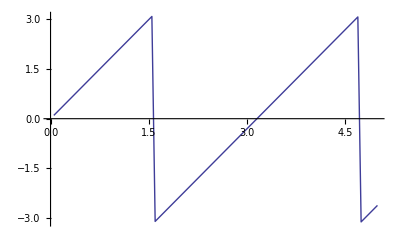

```mathematica
ListLinePlot[Transpose[{t3,meanXarg3}]]
```